# Histogram Equalization

## Objective

Histogram equalization is a technique used in image processing to form color adjustment using histogram data. In this MP you are asked to implement the histogram operation. You will then perform list reduction and scan on the histogram data to produce a histogram equalization formula that you will apply to the image.

## Instruction

Edit the code in the code tab to perform the following:

- Allocate device memory

- Copy host memory to device

- Initialize thread block and kernel grid dimensions

- Invoke CUDA kernel

- Copy results from device to host

- Free device memory

- Write the floating point to byte kernel

- Write the RGB to Gray Scale kernel

- Write the CUDA histogram kernel

- Perform the list convolution and reduction on the histogram output

- Write the histogram equalization kernel

- Write the byte to float point kernel

Remember that the output is an 8-bit image that must be saturated at 255. Begin with a naïve implementation then optimize it gradually. Keep a journal of every optimization you tried including the ones you abandoned because they limited you or worsened performance. This journal will help you answer the MP’s questions.

Instructions about where to place each part of the code is demarcated by the //@@ comment lines.

## Prototype (C code is interleaved)

This is a utility function for me that produces an overexposed image

```mathematica
overexpose[img_]:=Module[{f},
f[{h_,s_,b_}]:={h,s,Clip[b,{0.1,0.8}]};
ColorConvert[
ImageApply[f,ColorConvert[img,"HSB"]],
"RGB"
]
]
```

This is the starting input image. The image is stored in floating point representation and would be in a datastructure that they already used for image convolution. The datastructure is

typedef wbImage_t {
      int width;
      int height;
      int channels; /* always 3 */
      float * data
 } wbImage_t;
 
 they will have to write code that converts the float * data to unsigned * data.

```mathematica
overexposed=ImageResize[-Graphics-,512]
```

-Graphics-

This function performs rbg to gray scale mapping. In C it would look like:

unsigned char toRGB(float r, float g, float b) {
      return 0.21*r+0.71*g+0.07*b;
}
...
for (int ii = 0; ii < height; ii++) {
      for (jj = 0; jj < width; jj++) {
         int inputIdx = (ii*width + jj)*channels;
         gray[ii*width + jj] = toRGB(in[inputIdx + 0], in[inputIdx +1], in[inputIdx + 2]);
      }
}

```mathematica
toGrayScale[img_]:=Module[{f},
f[{r_,g_,b_}]:=0.21r+0.71 g+0.07b;
ImageApply[f,img]
]
```

The will then operate on the gray scale

```mathematica
goverexposed=toGrayScale[overexposed]
```

-Graphics-

```mathematica
{width,height}=ImageDimensions[goverexposed];
```

```mathematica
imgData=Flatten[ImageData[goverexposed,"Byte"]];
```

We then calculate the histogram on the image


memset(histo, 0, 256*sizeof(int));

for (int ii = 0; ii < width; ii++) {
   for (int jj = 0; jj < height; jj++) {
     histo[gray[ii*width +jj]]++;
   }
}

```mathematica
hist=Last[HistogramList[imgData,{0,256,1}]]/(width*height);
```

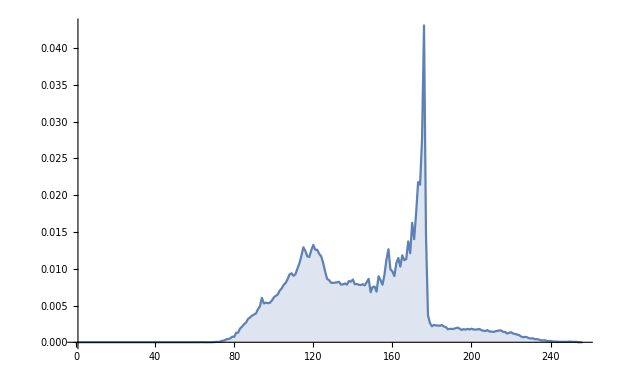

```mathematica
ListLinePlot[hist,Filling->Axis,PlotRange->Full]
```

They would then have to use the prefix sum operation (note they might try to do this on the CPU or GPU), since the histogram size is 256 it probably does not matter

accum = 0;
for (int ii = 0; ii < 256; ii++) {
     accum += hist[ii];
     cdf[ii] = accum;
}

```mathematica
cdf=Accumulate[hist];
```

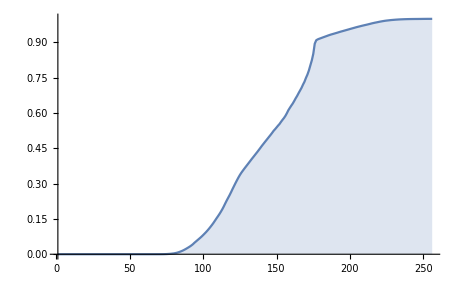

```mathematica
ListLinePlot[cdf,Filling->Axis,PlotRange->Full]
```

Then they need to perform a min reduction on the cdf data

minVal = 0;
for (int ii = 0; ii < 256; ii++) {
       minVal = min(minVal, cdf[ii]);
}

```mathematica
cdfmin=Min[cdf//.0->Infinity]
```

1/196608

With the cdf and cdfmin, they can construct the histogram equalization function

unsigned char histogramEqualize(int val, int * cdf, int cdfmin, int width, int height) {
    int val = 255 * ((cdf[val] - cdfmin)/(width * height - cdfmin));
    return (unsigned char) clip(val, 0, 255);
}

```mathematica
ClearAll[h]
```

```mathematica
Rescale[x,{1,cdfy},{1,cdfx}]
```

-(cdfx-cdfy)/(-1+cdfy)+((-1+cdfx) x)/(-1+cdfy)

```mathematica
h[v_]:=h[v]=Clip[Floor[255*(cdf[[v+1]]-cdfmin)/(1-cdfmin)],{0,255}]
```

This to show what the function looks like

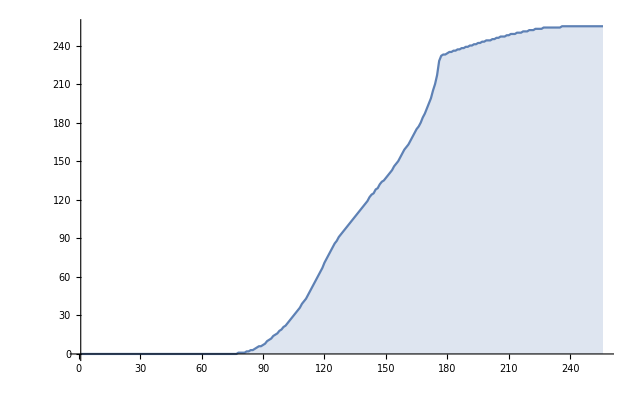

```mathematica
ListLinePlot[Table[h[x],{x,0,255,1}],Filling->Axis,PlotRange->Full]
```

Then they apply the histogram equalization function to each pixel value in the original RGB image:

for (int ii = 0; ii < height; ii ++) {
    for (int jj = 0; jj < width; jj++) {
          for (int kk = 0; kk < channels /* 3 */; kk++) {
              int idx = (ii * width + jj)*channels + kk;
              out[idx] = histogramEqualize(in[idx], cdf, cdfmin, width, height);
          }
    }
}

and get the image bellow

```mathematica
newImg=Image[Partition[Partition[h/@Flatten[ImageData[overexposed,"Byte"]],3],width],"Byte"]
```

-Graphics-

```mathematica
Flatten[h/@Flatten[ImageData[goverexposed,"Byte"]]]
```

{111,119,131,132,114,88,69,67,73,86,93,94,94,93,99,113,126,134,134,127,119,114,116,119,116,109,116,160,199,219,229,231,232,229,230,235,235,239,243,235,239,243,247,247,250,247,243,243,243,243,243,247,247,247,247,247,247,243,243,243,243,243,243,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,247,243,243,243,243,243,247,349525,118,199,211,213,214,216,216,217,218,218,218,217,216,216,213,211,210,207,204,202,199,192,193,202,208,211,212,215,220,223,226,226,225,224,223,222,222,220,218,217,216,215,216,217,208,193,178,188,202,183,142,83,60,51,53,51,56,56,53,50,50,53,53,51,50,49,47,49,53,50,45,43,42,46,53,51,53,53,54,49,47,46,43,39,37}
 |  |  |  |

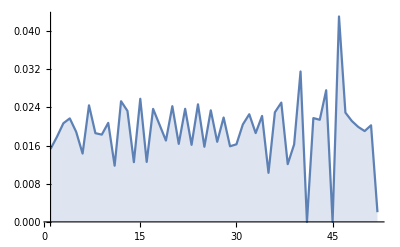

```mathematica
ListLinePlot[(Last@HistogramList[Flatten[h/@Flatten[ImageData[goverexposed,"Byte"]]]])/(width*height),Filling->Axis,PlotRange->Full]
```

```mathematica
newCDF=Accumulate[(Last@HistogramList[Flatten[ImageData[ColorConvert[newImg,"GrayScale"]]]])/(width*height)]
```

{1573/98304,6331/196608,10277/196608,4565/65536,2105/24576,6781/65536,2963/24576,4559/32768,7693/49152,8623/49152,613/3072,43747/196608,48169/196608,8869/32768,14633/49152,31829/98304,22743/65536,17963/49152,4711/12288,78853/196608,13819/32768,21571/49152,89779/196608,31071/65536,96643/196608,50113/98304,34561/65536,53359/98304,109645/196608,56521/98304,58699/98304,30547/49152,125621/196608,16111/24576,66205/98304,33841/49152,23021/32768,17641/24576,143213/196608,76229/98304,176257/196608,88343/98304,44309/49152,88987/98304,22355/24576,11/12,45995/49152,187765/196608,23957/24576,196003/196608,1}

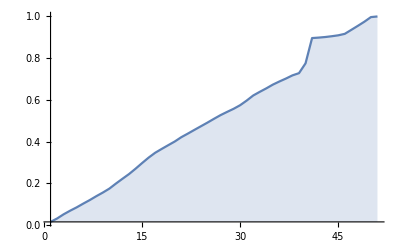

```mathematica
ListLinePlot[newCDF,Filling->Axis,PlotRange->Full]
```

Compare the two images with their histograms

```mathematica
Grid[{{
Legended[Image[overexposed,ImageSize->Scaled[1/2]],Placed[ImageHistogram[overexposed,Appearance->"Transparent",ImageSize->Scaled[1/2],FrameTicks->True],Below]],
Legended[Image[newImg,ImageSize->Scaled[1/2]],Placed[ImageHistogram[newImg,Appearance->"Transparent",ImageSize->Scaled[1/2],FrameTicks->True],Below]]
}}]
```

-Graphics- | -Graphics-

## Other Outputs

-Graphics- | -Graphics-

-Graphics- | -Graphics-

-Graphics- | -Graphics-

«1 more identical outputs»